```mathematica
Quit
```

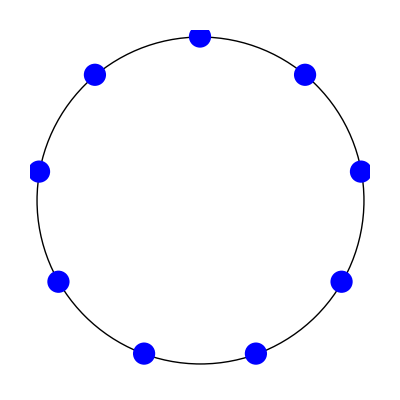

```mathematica
Npts=9;
Graphics[Ginit={Circle[],PointSize[.04],Blue,Point@CirclePoints[Npts]}]
```

```mathematica
I2=IdentityMatrix[2];
hp=({{1, 0}, {0, -1}});
hx=({{0, 1}, {1, 0}});
eps=0.1;
```

```mathematica
phis=2π Range[0,4]/4;
```

```mathematica
extraPlotFac=1.05;
pr=PlotRange->extraPlotFac(1+eps){{-1,1},{-1,1}};
```

```mathematica
frameshp =Graphics[GeometricTransformation[Ginit,AffineTransform[I2+eps Sin[#] hp]],pr]&/@phis;
frameshx=Graphics[GeometricTransformation[Ginit,AffineTransform[I2+eps Sin[#] hx]],pr]&/@phis;
textrow=Text[Style[Row[{"ϕ=",#}],FontSize->20]]&/@phis;
```

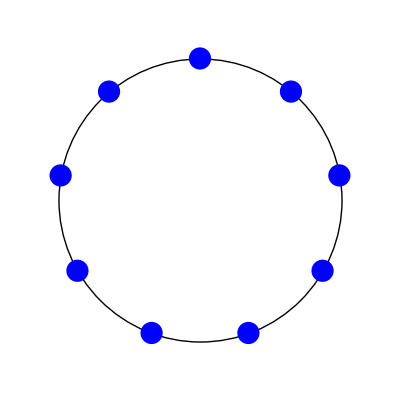
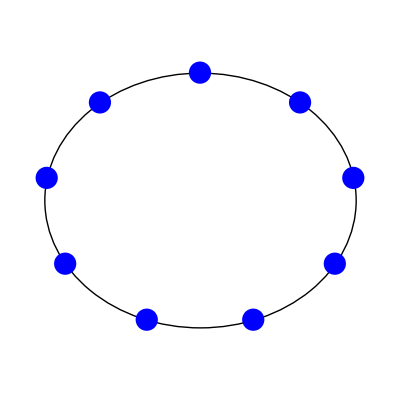
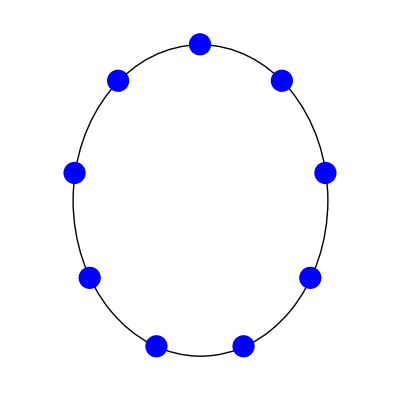
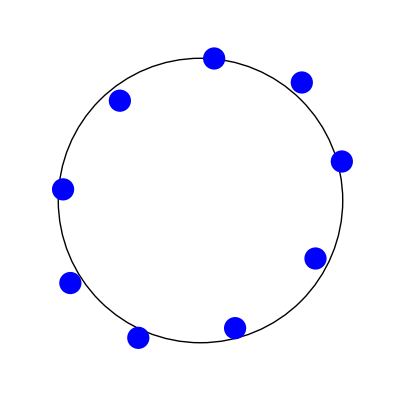
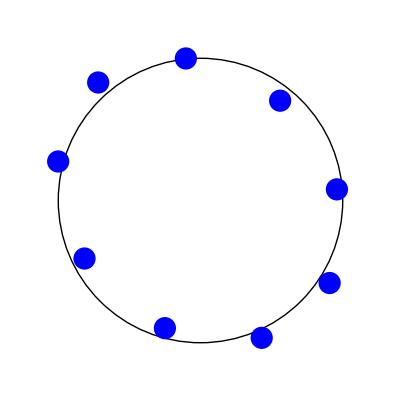
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
ϕ=0 | ϕ=π/2 | ϕ=π | ϕ=(3 π)/2 | ϕ=2 π

```mathematica
finalgrid=Grid[{frameshp,frameshx,textrow}]
```

```mathematica
Export[NotebookDirectory[]<>"polarizations.pdf",finalgrid]
```

/Users/leo/Documents/calculations/gravitational-wave-polarizations-figure/polarizations.pdf